## A367083: List of powers of 3 and powers of 4, in increasing order, starting with a(0) = 3^0 = 4^0 = 1.

### MATHEMATICA PROGRAM:

```mathematica
With[{max=2*10^10},Union[3^Range[0,Log[3,max]],4^Range[0,Log[4,max]]]] (*Paul F.Marrero Romero,Nov 14 2023*)
```

{1,3,4,9,16,27,64,81,243,256,729,1024,2187,4096,6561,16384,19683,59049,65536,177147,262144,531441,1048576,1594323,4194304,4782969,14348907,16777216,43046721,67108864,129140163,268435456,387420489,1073741824,1162261467,3486784401,4294967296,10460353203,17179869184}

### Formula:

Union of  A000244 and A000302.  - 	M. F. Hasler, Nov 03 2023

### Plot section:

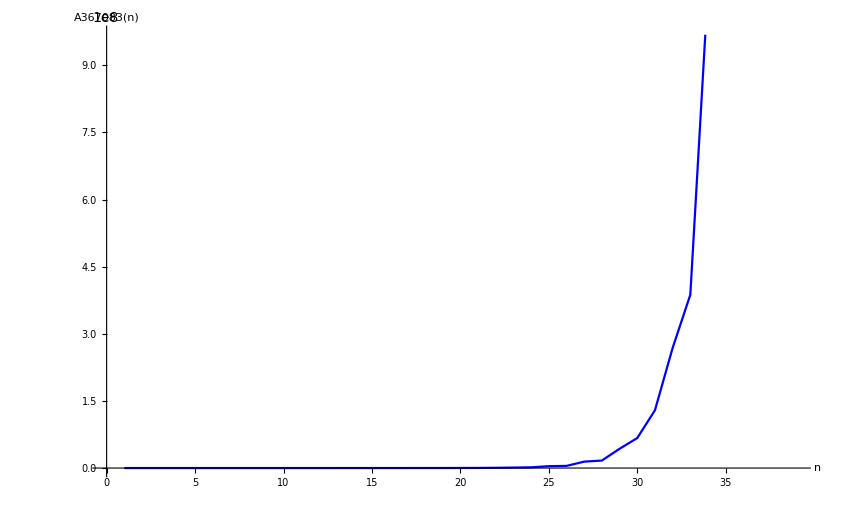

```mathematica
ListPlot[ With[{max=2*10^10},Union[3^Range[0,Log[3,max]],4^Range[0,Log[4,max]]]], Joined->True, PlotStyle-> Blue, AxesLabel->{"n","A367083(n)"}, LabelStyle->Directive[Black,Bold]]
```

### References:

M. F. Hasler, List of powers of 3 and powers of 4, in increasing order, starting with a(0) = 3^0 = 4^0 = 1., Entry A367083 in The On-Line Encyclopedia of Integer Sequences, https://oeis.org/A367083